```mathematica
f[x_]:=x^2
```

```mathematica
T=Integrate[x^2,{x,0,3}]
```

9

```mathematica
Int1[f_,a_,b_,N1_]:=Module[{g=f,a1=a,b1=b,N2=N1,l,h=(b-a)/N1},l=h*Sum[g[a1+i*h],{i,0,N2}]]
```

```mathematica
Int1[f,0,3,100]//N
```

9.13545

```mathematica
M=Table[Abs[T-Int1[f,0,3,n]],{n,1,100}];
```

```mathematica
j1=ListPlot[M];
```

```mathematica
Int2[f_,a_,b_,N1_]:=Module[{g1=f,a2=a,b2=b,N3=N1,h=(b-a)/N1},h*(g1[a2]+g1[b2])/2+h*Sum[g1[a2+i*h],{i,1,N3-1}]]
```

```mathematica
Int2[f,0,3,100]//N;
```

```mathematica
M1=Table[Abs[T-Int2[f,0,3,n]],{n,1,100}];
```

```mathematica
j2=ListPlot[M1,PlotStyle->Red];
```

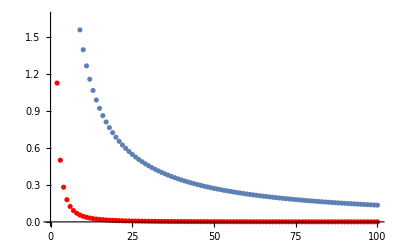

```mathematica
Show[j1,j2]
```